# Midterm 3

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

## Problem 5

Two Martians are having a water balloon launching contest. They are standing on a position that has a colatitude of 120 degrees (meaning a polar angle of 120 degrees from the geographic north pole). A small target has been placed 2 km directly west of where they are standing. The first Martian, who has taken Physics 121 but not Physics 321, decides to launch the balloon due west with a 45 degree angle above the horizontal and an initial launch speed of 86.267 m/s. The second Martian, who has taken Physics 321, smiles to herself, already knowing that she will win the competition because her less-experienced friend does not know about the Coriolis force. The goal of this problem is to determine how far away the water balloon lands from the target. The figures below illustrate the situation.
-Graphics-



-Graphics-


-Graphics-

Important information:
Let z be up, x be due east, and y be due north (this is the convention used in the textbook and lecture when deriving the equations for projectile motion).
The acceleration due to gravity near the surface of Mars is 3.721 m/s^2 (you may assume this includes any minor modifications due to the centrifugal force).
The atmosphere on Mars is very thin, so you may neglect any drag forces.
Mars takes 24.6598 hours to complete one rotation about its axis.

m = 0.5 kg is the mass of the water balloon.
theta = 120 degrees is the angle from the geographic north pole.
Omega is the angular speed of Mars (you must calculate this).

```mathematica
Quit[]
Clear["`*"]
```

## Part A: Qualitative Analysis (5 points)

Will the landing point of the water balloon be south of the target or north of the target?
North of the target

Will the landing point of the water balloon be east of the target or west of the target?
East of the target

## Part B: Set up the equations and initial conditions (7 points)

Various values are given to you below, but you must calculate the value for Omega based on information given in the problem. (1 point)

```mathematica
m=0.5;
g=3.721;
theta=120*Pi/180; (* colatitude *)
alpha=45*Pi/180; (* launch angle *)
v0=86.267; (* launch speed *)
Omega=(24.6598/(2*Pi)*60*60)^-1; (* angular speed of Mars *)
```

Now write down the equations of motion appropriate for this situation, taking into account the rotation of Mars. (3 points)

```mathematica
Xeq=x''[t]==2*Omega*(y'[t]*Cos[theta]-z'[t]*Sin[theta]);
Yeq=y''[t]==-2*Omega*x'[t]*Cos[theta];
Zeq=z''[t]==-g+2*Omega*x'[t]*Sin[theta];
```

And now provide the initial conditions. (3 points)

```mathematica
x0=0;
xdot0=v0*Cos[alpha];
y0=0;
ydot0=0;
z0=0;
zdot0=v0*Sin[alpha];
```

## Part C: Solve for the trajectory and interpret it (8 points)

Solve the equations. (2 points)

```mathematica
sol=NDSolve[{Xeq,Yeq,Zeq,x[0]==x0,y[0]==y0,z[0]==z0,x'[0]==xdot0,y'[0]==ydot0,z'[0]==xdot0},{x,y,z},{t,0,40}];
```

Determine how far it misses in the x direction. (2 points)

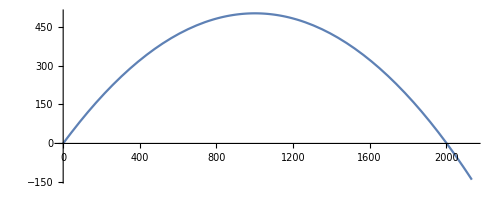

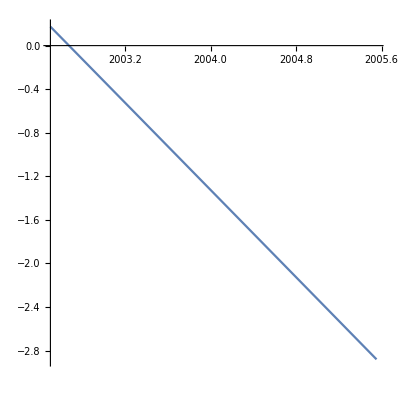

```mathematica
ParametricPlot[{x[t],z[t]}/.sol,{t,0,35}]

(* Now zoom in as appropriate to find your answer to the nearest 0.1 meters *)
ParametricPlot[{x[t],z[t]}/.sol,{t,32.85,32.9}]
```

Answer to the nearest 0.1 m: Δx = landing value - target value = landing value - (- 2000 m) = 2002.7-2000 = 2.7

Determine how far it misses in the y direction. (2 points)

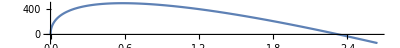

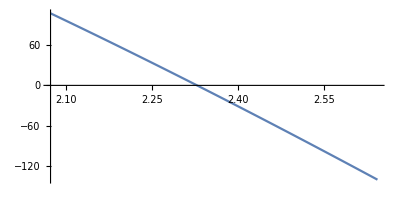

```mathematica
ParametricPlot[{y[t],z[t]}/.sol,{t,0,35},AspectRatio->0.1]
(* Now zoom in as appropriate to find your answer to the nearest 0.1 meters *)
ParametricPlot[{y[t],z[t]}/.sol,{t,31,35},AspectRatio->0.5]
```

Answer to the nearest 0.1 m: Δy = landing value - target value = landing value - 0 = 2.3

In terms of the cardinal directions (north, south, east, west), describe where the landing point of the water balloon is relative to the target. (2 points) 
Northeast

## Additional work for any of the written problems (label each one clearly)

```mathematica
Quit[]
Clear["`*"]
```

```mathematica
(* Written Problem 3 *)
sig = M/(3*L^2/4);
Jxx= Integrate[x^2*sig,{x,0,L},{y,0,(L/2)/L*x}]+Integrate[x^2*sig,{x,0,L},{y,0,-x}];
Jyy= Integrate[y^2*sig,{x,0,L},{y,0,((L/2)/L*x)}]+Integrate[y^2*sig,{x,0,L},{y,0,-L/L*x}];
Jxy= Integrate[x*y*sig,{x,0,L},{y,0,(L/2)/L*x}]+Integrate[x*y*sig,{x,0,L},{y,0,-L/L*x}];
MI={{Jyy,-Jxy,0},{-Jxy,Jxx,0},{0,0,Jxx+Jyy}};
MI//MatrixForm
sols=Eigensystem[MI]
eq1=1/144 (-19-5 √37) L^2 M*w1'[t]==(-(19 L^2 M)/72-1/144 (-19+5 √37) L^2 M)*w2[t]*w3[t]
eq2=-(19 L^2 M)/72*w2'[t]==((1/144 (-19+5 √37) L^2 M)-1/144 (-19-5 √37) L^2 M)*w3[t]*w1[t]
eq3=1/144 (-19+5 √37) L^2 M*w3'[t]==(1/144 (-19-5 √37) L^2 M-(19 L^2 M)/72)*w1[t]*w2[t]
DSolve[{eq1,eq2,eq3},{w1[t],w2[t],w3[t]},t]
```

(-(7 L^2 M)/72 | -(5 L^2 M)/24 | 0
-(5 L^2 M)/24 | -(L^2 M)/6 | 0
0 | 0 | -(19 L^2 M)/72)

{{1/144 (-19-5 √37) L^2 M,-(19 L^2 M)/72,1/144 (-19+5 √37) L^2 M},{{1/6 (-1+√37),1,0},{0,0,1},{1/6 (-1-√37),1,0}}}

1/144 (-19-5 √37) L^2 M w1'[t]==(-(19 L^2 M)/72-1/144 (-19+5 √37) L^2 M) w2[t] w3[t]

-19/72 L^2 M w2'[t]==(-1/144 (-19-5 √37) L^2 M+1/144 (-19+5 √37) L^2 M) w1[t] w3[t]

1/144 (-19+5 √37) L^2 M w3'[t]==(-(19 L^2 M)/72+1/144 (-19-5 √37) L^2 M) w1[t] w2[t]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{w1[t]→(√(38/5) √C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])])/37^(1/4),w2[t]→-(√(38 C[1]-38 C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2))/(√19),w3[t]→-√(2 C[2]+(38 C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(19-5 √37)+(2166 C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(5 √37 (19-5 √37)))},{w1[t]→(√(38/5) √C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])])/37^(1/4),w2[t]→(√(38 C[1]-38 C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2))/(√19),w3[t]→√(2 C[2]+(38 C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(19-5 √37)+(2166 C[1] JacobiSN[1/19 (37^(1/4) √190 t √C[2]-37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(5 √37 (19-5 √37)))},{w1[t]→(√(38/5) √C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])])/37^(1/4),w2[t]→-(√(38 C[1]-38 C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2))/(√19),w3[t]→√(2 C[2]+(38 C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(19-5 √37)+(2166 C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(5 √37 (19-5 √37)))},{w1[t]→(√(38/5) √C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])])/37^(1/4),w2[t]→(√(38 C[1]-38 C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2))/(√19),w3[t]→-√(2 C[2]+(38 C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(19-5 √37)+(2166 C[1] JacobiSN[1/19 (-37^(1/4) √190 t √C[2]+37^(1/4) √190 √C[2] C[3]),(19 (57+5 √37) C[1])/(5 (185-19 √37) C[2])]^2)/(5 √37 (19-5 √37)))}}

```mathematica
(* Written Problem 3 *)
sig = M/(3*L^2/4);
Jxx= Integrate[1/2 x^3*sig,{x,0,L}]+Integrate[-x^3*sig,{x,0,L}];
Jyy= Integrate[x^3/24*sig,{x,0,L}]+Integrate[-x^3/3*sig,{x,0,L}];
Jxy= Integrate[x*x^2/8*sig,{x,0,L}]+Integrate[x*x^2/2*sig,{x,0,L}];
MI={{Jyy,-Jxy,0},{-Jxy,Jxx,0},{0,0,Jxx+Jyy}};
MI//MatrixForm
sols=Eigensystem[MI]
eq1=MI[[1]]*w1'[t]==(MI[[2]]-MI[[3]])*w2[t]*w3[t]
eq2=MI[[2]]*w2'[t]==(MI[[3]]-MI[[1]])*w3[t]*w1[t]
eq3=MI[[3]]*w3'[t]==(MI[[1]]-MI[[2]])*w1[t]*w2[t]
DSolve[{eq1,eq2,eq3},{w1[t],w2[t],w3[t]},t]
```

(-(7 L^2 M)/72 | -(5 L^2 M)/24 | 0
-(5 L^2 M)/24 | -(L^2 M)/6 | 0
0 | 0 | -(19 L^2 M)/72)

{{1/144 (-19-5 √37) L^2 M,-(19 L^2 M)/72,1/144 (-19+5 √37) L^2 M},{{1/6 (-1+√37),1,0},{0,0,1},{1/6 (-1-√37),1,0}}}

{-7/72 L^2 M w1'[t],-5/24 L^2 M w1'[t],0}=={-5/24 L^2 M w2[t] w3[t],-1/6 L^2 M w2[t] w3[t],19/72 L^2 M w2[t] w3[t]}

{-5/24 L^2 M w2'[t],-1/6 L^2 M w2'[t],0}=={7/72 L^2 M w1[t] w3[t],5/24 L^2 M w1[t] w3[t],-19/72 L^2 M w1[t] w3[t]}

{0,0,-19/72 L^2 M w3'[t]}=={1/9 L^2 M w1[t] w2[t],-1/24 L^2 M w1[t] w2[t],0}

DSolve::overdet: There are fewer dependent variables than equations, so the system is overdetermined.

DSolve[{{-7/72 L^2 M w1'[t],-5/24 L^2 M w1'[t],0}=={-5/24 L^2 M w2[t] w3[t],-1/6 L^2 M w2[t] w3[t],19/72 L^2 M w2[t] w3[t]},{-5/24 L^2 M w2'[t],-1/6 L^2 M w2'[t],0}=={7/72 L^2 M w1[t] w3[t],5/24 L^2 M w1[t] w3[t],-19/72 L^2 M w1[t] w3[t]},{0,0,-19/72 L^2 M w3'[t]}=={1/9 L^2 M w1[t] w2[t],-1/24 L^2 M w1[t] w2[t],0}},{w1[t],w2[t],w3[t]},t]

```mathematica
Quit[]
Clear["`*"]
```

```mathematica
(* Written Problem 4 *)
U=Simplify[1/2*k*x1^2+1/2*k*(x2-x1)^2+1/2*k*(x3-x2)^2+1/2*k*x3^2];
T=1/2*m*(x1dot^2+x2dot^2+x3dot^2);
L=T-U;
rule={x1->x1[t],x2->x2[t],x3-> x3[t],x1dot->x1'[t],x2dot-> x2'[t],x3dot-> x3'[t]};
dLdx1= D[L,x1]/.rule;
dLdx2= D[L,x2]/.rule;
dLdx3= D[L,x3]/.rule;
Px1= D[L,x1dot]/.rule;
Px2= D[L,x2dot]/.rule;
Px3= D[L,x3dot]/.rule;
x1eq=dLdx1==D[Px1,t]
x2eq=dLdx2==D[Px2,t]
x3eq=dLdx3==D[Px3,t]
```

```mathematica
(* Written Problem 4 Continued *)
M={{m,0,0},{0,m,0},{0,0,m}};
K={{2*k,-k,0},{-k,2*k,-k},{0,-k,2*k}};
N[Eigensystem[Inverse[M].K]]
```